```mathematica
Clear["Global`*"];

d = 4;
Δ = d-1;
Print["y = η_1^(-1/2)"]
n = 70;

Print["LHS = "]
lhs= Normal[Series[Exp[(1)y^3(1-y^2)^(-3/2)],{y,0,n}]] ;
Print["Expanded upto y^n i.e. η_1^(-n/2)"]
Print["Defect expansion Coefficients = "]
dec = Array[c,n-Δ+2,0];
Print["c[0] -> Zero dimension coefficient (Contribution of identity operator)"]
Print["c[1] -> First non-zero coefficient (for Δ_o = Δ_ϕ), c[2] -> coefficient for Δ_o = Δ_ϕ+1, and so on ..."]

F[a_]:=Normal[Series[y^a Hypergeometric2F1[a/2,(a+1)/2,1+a-(d/2),y^2],{y,0,n}]];
Print["Conformal Blocks upto Δ_o = n and expanded upto y^n i.e. η_1^(-n/2) = "]
cb = Prepend[Table[F[i],{i,Δ,n}],F[0]];
Print["RHS = "]
rhs = Collect[Dot[dec,cb],x];

s = NSolve[Thread[Equal[CoefficientList[lhs,y][[Δ+1;;]],CoefficientList[rhs,y][[Δ+1;;]]]]]
```

y = η_1^(-1/2)

LHS =

Expanded upto y^n i.e. η_1^(-n/2)

Defect expansion Coefficients =

c[0] -> Zero dimension coefficient (Contribution of identity operator)

c[1] -> First non-zero coefficient (for Δ_o = Δ_ϕ), c[2] -> coefficient for Δ_o = Δ_ϕ+1, and so on ...

Conformal Blocks upto Δ_o = n and expanded upto y^n i.e. η_1^(-n/2) =

RHS =

{{c[1]→1.,c[2]→7.54313×10^-14,c[3]→-1.16254×10^-12,c[4]→0.5,c[5]→2.53577×10^-12,c[6]→0.45,c[7]→0.166667,c[8]→0.267857,c[9]→0.28125,c[10]→0.171875,c[11]→0.275,c[12]→0.158203,c[13]→0.211458,c[14]→0.160907,c[15]→0.152344,c[16]→0.147092,c[17]→0.114966,c[18]→0.11932,c[19]→0.091941,c[20]→0.0898182,c[21]→0.0740698,c[22]→0.0657508,c[23]→0.0577745,c[24]→0.0481366,c[25]→0.0432288,c[26]→0.0353928,c[27]→0.0312949,c[28]→0.0258889,c[29]→0.0222034,c[30]→0.0186539,c[31]→0.0155835,c[32]→0.0131838,c[33]→0.0108573,c[34]→0.00914854,c[35]→0.00750316,c[36]→0.00625437,c[37]→0.00513202,c[38]→0.00422676,c[39]→0.00346897,c[40]→0.00282974,c[41]→0.00231688,c[42]→0.00187817,c[43]→0.00153023,c[44]→0.0012358,c[45]→0.00100064,c[46]→0.000805913,c[47]→0.000648558,c[48]→0.000520855,c[49]→0.000416921,c[50]→0.000333711,c[51]→0.000265988,c[52]→0.00021201,c[53]→0.000168358,c[54]→0.000133691,c[55]→0.000105855,c[56]→0.0000836391,c[57]→0.000065986,c[58]→0.0000520217,c[59]→0.0000409379,c[60]→0.0000320727,c[61]→0.0000251459,c[62]→0.0000197476,c[63]→0.0000154131,c[64]→0.0000119132,c[65]→9.32935×10^-6,c[66]→7.42782×10^-6,c[67]→5.6929×10^-6,c[68]→4.16366×10^-6}}

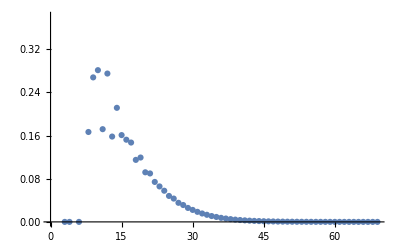

```mathematica
ListPlot[dec/.s[[1]]]
```